```mathematica
tockeN[stTock_]:=Table[{RandomReal[],RandomReal[]},{stTock}]
```

```mathematica
krog[{x_,y_}]:=x^2+y^2==1
```

```mathematica
Get["C:\\Users\\lukau\\Desktop\\NRO\\DN2\\priblizekPi.m"]
```

```mathematica
stTock=1000;
```

```mathematica
priblizek=priblizekPi[stTock];
priblizek=N[priblizek]
```

3.144

```mathematica
tocke=tockeN[stTock];
tockeKrog=Select[tocke,Norm[#]<=1&];
kroznica=Select[tocke,krog];
zunaj=Complement[tocke,Join[tockeKrog,kroznica]];
```

```mathematica
p1=ListPlot[tockeKrog,PlotStyle->Blue,AspectRatio->1,PlotRange->{{0,1},{0,1}},PlotLegends->{"Točke v krogu"}];
p2=ListPlot[zunaj,PlotStyle->Red,PlotLegends->{"Točke zunaj kroga"}];
p3=Graphics[{EdgeForm[Black],FaceForm[None],Circle[{0,0},1]},Axes->True,AspectRatio->1,PlotRange->{{0,1},{0,1}}];
```

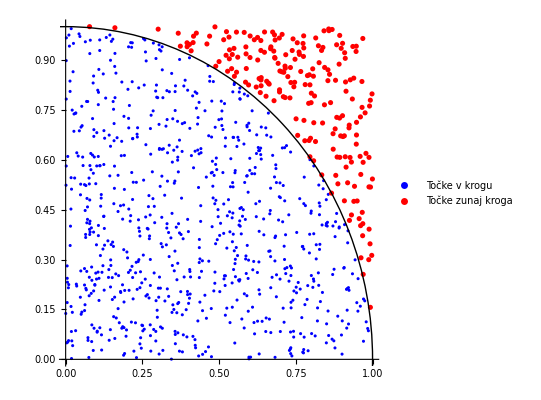

```mathematica
Show[p1,p2,p3,PlotRange->{{0,1},{0,1}}]
```